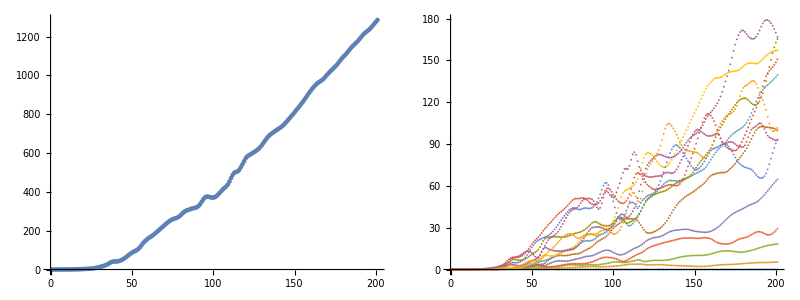

```mathematica
QAinitial="/Users/rogeriojorge/local/some_optimizations/GS2_SIMSOPT_ITG/nonlinear_nfp2_QA_initial_ln1.0_lt3.0/gs2Input_ln1.0lt3.0.out.nc";
QAfinal="/Users/rogeriojorge/local/some_optimizations/GS2_SIMSOPT_ITG/nonlinear_nfp2_QA_test_ln1.0_lt3.0/gs2Input_ln1.0lt3.0.out.nc";
QHinitial="/Users/rogeriojorge/local/some_optimizations/GS2_SIMSOPT_ITG/nonlinear_nfp2_QH_initial_ln1.0_lt3.0/gs2Input_ln1.0lt3.0.out.nc";
QHfinal="/Users/rogeriojorge/local/some_optimizations/GS2_SIMSOPT_ITG/nonlinear_nfp2_QH_test_ln1.0_lt3.0/gs2Input_ln1.0lt3.0.out.nc";

fluxQAin=Import[QAinitial,{"Datasets","es_heat_flux"}]//Transpose;
fluxQAfin=Import[QAfinal,{"Datasets","es_heat_flux"}]//Transpose;
fluxQHin=Import[QHinitial,{"Datasets","es_heat_flux"}]//Transpose;
fluxQHfin=Import[QHfinal,{"Datasets","es_heat_flux"}]//Transpose;

ListPlot[{fluxQAin,fluxQAfin,fluxQHin,fluxQHin},ImageSize->Medium]
```